#### Problem 1.0

```mathematica
addem[a_,b_] := Module[{}, a = a+b; Return[a];]
```

```mathematica
addem[3,4]
```

Set::setraw: Cannot assign to raw object 3.

3

```mathematica
addem2[a_,b_] := Module[{c, retval}, c = a+b; Return[retval]]
```

```mathematica
addem2[3,4]
```

retval$2111

#### Problem 1.1

```mathematica
Bisection[F_,xl0_, xr0_, ϵ_] := Module[{xl, xr, xm},
xl = xl0;
xr = xr0;
xm = (1/2)(xl + xr);
While[Abs[F[xm]] > ϵ,
If[F[xm] F[xr] < 0,
xl = xm,
xr = xm
];
xm = (1/2)(xl + xr);
];
Return[xm];
]
```

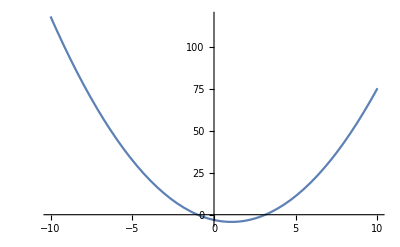

```mathematica
Plot[Function[x, (x-Pi)(x+1)][x], {x, -10, 10}]
```

```mathematica
N[Bisection[Function[x, (x-Pi)(x+1)], 0, 10, 10^-10]]
N[Bisection[Function[x, (x-Pi)(x+1)], -10, 0, 10^-10]]
```

3.14159

-1.

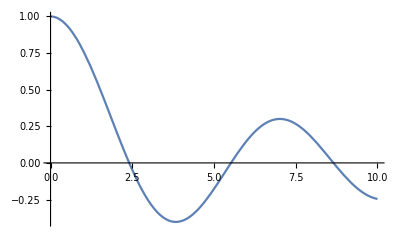

```mathematica
Plot[BesselJ[0,x], {x, 0, 10}]
```

```mathematica
N[Bisection[Function[x, BesselJ[0,x]], 0, 3, 10^-10]]
N[Bisection[Function[x, BesselJ[0,x]], 3, 6, 10^-10]]
```

2.40483

5.52008

#### Problem 1.2

```mathematica
r = {0,0,0};
R = 10^5;
ω = 2000;
t = 0;
d = 1;
c = 3 10^8;
```

```mathematica
w[t_] := {R Cos[ω t], 0, d ω t};
F[tr_] := c (t-tr) - Sqrt[(r-w[tr]).(r-w[tr])]
```

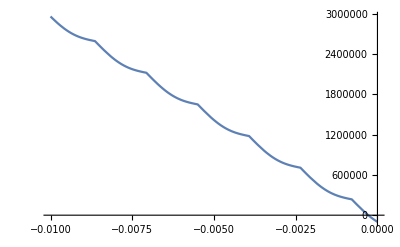

```mathematica
Plot[F[x], {x, -.01, 0}]
```

```mathematica
N[Bisection[F, -1, 0, 10^-10]]
```

-0.000281785

The position at this retarded time is

```mathematica
w[-0.00028178460211737526]
```

{84535.4,0,-0.563569}

If we ignored the retarded time, the position would be

```mathematica
w[0]
```

{100000,0,0}

The distance between these positions is

```mathematica
Norm[w[-0.00028178460211737526]-w[0]]
```

15464.6

#### Problem 1.3

```mathematica
c3=1;
q4Piϵ0 = 1;
```

```mathematica
VField[x_,y_,z_,t_,w_,ϵ_] := Module[{r, F, tr, R, V},
r = {x,y,z};
F = Function[X, c3(t - X) - Norm[r-w[X]]];
tr = Bisection[F, -10, t, ϵ];
R = Norm[r-w[tr]];
V =q4Piϵ0/R;
Return[V];
]
```

```mathematica
VFieldFast = Compile[{x,y,z,t,{w, _Function},ϵ}, VField[x,y,z,t,w,ϵ]];
```

Compile::ctyp2: Invalid type or rank specification in {w,_Function}.

```mathematica
d = 0.05; ω = 5; ϵ = 10^-10;
w[t_] := {0, d Cos[ω t] , 0};
```

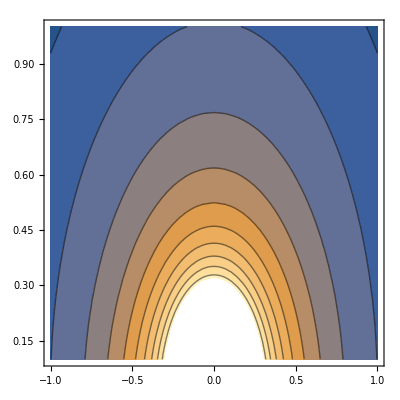

```mathematica
ContourPlot[VField[x,y,0,t,w,ϵ],{x,-1,1},{y,.1,1}]
```

```mathematica
data=Monitor[Table[ContourPlot[VField[x,y,0,t,w,ϵ],{x,-1,1},{y,.1,1}],{t,0+0.0001,8 Pi/5+.0001,(2 Pi/5)/5}], ProgressIndicator[t, {0, (8 Pi/5)}]];
```

```mathematica
ListAnimate[data]
```